Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

2 - 7 Function Values
Find ⅇ^z in the form u + ⅈ v and Abs[ⅇ^z] if z equals

3.  2 π I (1 + I)

```mathematica
ComplexExpand[ⅇ^(2 π I (1+I))]
```

ⅇ^(-2 π)

```mathematica
N[%]
```

0.00186744

5.  2 + 3 π I

```mathematica
ComplexExpand[ⅇ^(2+3 π I)]
```

-ⅇ^2

```mathematica
N[%]
```

-7.38906

7. √2+1/2 π ⅈ

```mathematica
ComplexExpand[ⅇ^(√2+1/2 π ⅈ)]
```

ⅈ ⅇ^(√2)

```mathematica
N[%]
```

0.+4.11325 ⅈ

8 - 13 Polar Form. Write in exponential form, numbered line (6), p. 631:

9.  4 + 3 I

```mathematica
Clear["Global`*"]
```

```mathematica
z=4+3 I
```

4+3 ⅈ

Restating the polar form described in numbered line (6),

```mathematica
Abs[z] ⅇ^(ⅈ Arg[z])
```

5 ⅇ^(ⅈ ArcTan[3/4])

```mathematica
N[Arg[z]]
```

0.643501

11. - 6.3

```mathematica
Clear["Global`*"]
```

This one takes a little “identity crisis”, as shown in numbered line (8) on p. 631,

```mathematica
z==-6.3==6.3(-1)==6.3(ⅇ^(π ⅈ))
```

True

13.  1 + I

```mathematica
Clear["Global`*"]
```

```mathematica
z=1+I
```

1+ⅈ

```mathematica
Abs[z] ⅇ^(ⅈ Arg[z])
```

√2 ⅇ^((ⅈ π)/4)

14 - 17 Real and Imaginary Part. Find Re and Im of

15. Exp[z^2]

This problem is handled manually mostly.

```mathematica
Clear["Global`*"]
```

```mathematica
Expand[Exp[z^2]/.z->(x+ⅈ y)]
```

ⅇ^((x+ⅈ y)^2)

```mathematica
int1=Exp[Expand[(x+ⅈ y)^2]]
```

ⅇ^(x^2+2 ⅈ x y-y^2)

```mathematica
int1==Exp[x^2-y^2]Exp[2 ⅈ x y]
```

True

Because of identity in numbered line (5) on p. 631 I can write,

```mathematica
int2==Exp[x^2-y^2](Cos[2 x y]+ⅈ Sin[2 x y]);
```

And therefore, just splitting up the expression,

```mathematica
realz==Exp[x^2-y^2](Cos[2 x y]);
```

```mathematica
imagz==Exp[x^2-y^2]( Sin[2 x y]);
```

17.  Exp[z^3]

```mathematica
Clear["Global`*"]
```

```mathematica
Expand[Exp[z^3]/.z->(x+ⅈ y)]
```

ⅇ^((x+ⅈ y)^3)

```mathematica
int1=Exp[Expand[(x+ⅈ y)^3]]
```

ⅇ^(x^3+3 ⅈ x^2 y-3 x y^2-ⅈ y^3)

In order to apply numbered line (5), I need to isolate terms containing ⅈ,

```mathematica
int1==Exp[x^3-3x y^2]Exp[3 ⅈ x^2 y-ⅈ y^3];
```

And then I can apply the identity,

```mathematica
int2==Exp[x^3-3x y^2](Cos[3 x^2 y- y^3]+ⅈ Sin[3 x^2 y- y^3]);
```

so that

```mathematica
realz=Exp[x^3-3x y^2](Cos[3 x^2 y- y^3]);
```

```mathematica
imagz=Exp[x^3-3x y^2]( Sin[3 x^2 y- y^3]);
```

In this case the text does not give an answer for the imaginary part.

19 - 22 Equations. Find all solutions and graph some of them in the complex plane.

19.  ⅇ^z=1

The below effort looks stupid, but it’s all I could come up with.

```mathematica
Clear["Global`*"]
```

```mathematica
gs[z]=Exp[z]
```

ⅇ^z

```mathematica
myt=Solve[gs[z]==1,z]
```

{{z→ConditionalExpression[2 ⅈ π C[1],C[1]∈Integers]}}

```mathematica
myt2=myt/.C[1]->d
```

{{z→ConditionalExpression[2 ⅈ d π,d∈Integers]}}

```mathematica
myt3=Table[myt2,{d,0,10}]
```

{{{z→0}},{{z→2 ⅈ π}},{{z→4 ⅈ π}},{{z→6 ⅈ π}},{{z→8 ⅈ π}},{{z→10 ⅈ π}},{{z→12 ⅈ π}},{{z→14 ⅈ π}},{{z→16 ⅈ π}},{{z→18 ⅈ π}},{{z→20 ⅈ π}}}

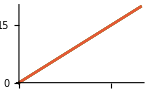

```mathematica
Plot[myt3,{z,0,20},ImageSize->150]
```

```mathematica
myt4=Flatten[myt3]
```

{z→0,z→2 ⅈ π,z→4 ⅈ π,z→6 ⅈ π,z→8 ⅈ π,z→10 ⅈ π,z→12 ⅈ π,z→14 ⅈ π,z→16 ⅈ π,z→18 ⅈ π,z→20 ⅈ π}

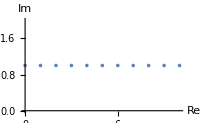

```mathematica
ListPlot[Table[{d,Exp[2 ⅈ d π]},{d,0,10}],AxesLabel->{"Re","Im"},ImageSize->200]
```